```mathematica
s=NDSolve[{y'[x]==9*x^2*y[x]+(x^5+ x^2)*y[x]^(2/3),y[0.1]==0.1},y,{x,0.1,1}]
```

{{y→InterpolatingFunction[…]}}

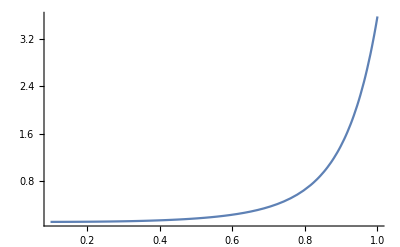

```mathematica
Plot[Evaluate[y[x]/.s],{x,0.1,1},PlotRange->All]
```